# Cyclic Voltammetry - Numerical Integration

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
Needs["Notation`"];
```

```mathematica
Symbolize[Subscript[r, _]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
BaseStyle->Directive[FontFamily-> "Arial",10,Plain],
FrameLabel->None,
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
cvTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];

cvTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];
```

```mathematica
option1={
PlotRange-> {{0,init-switch}, {0, -0.5}},
AxesOrigin-> {0,0},
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks:>  {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["σ t",FontFamily-> "Times New Roman",FontSize-> 12, FontColor-> Black,FontSlant->Italic],
Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}};
```

```mathematica
option2={
PlotRange-> {{switch,init}, {0, -0.5}},
AxesOrigin-> {switch,0},
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks:>  {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
Joined-> True,
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black, FontSlant->Italic], 
Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}};
```

```mathematica
option3={
PlotRange-> {{init-switch,final}, {0, -0.5}},
AxesOrigin-> {init-switch,0},
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
StyleForm["σ t",FontFamily-> "Times New Roman",FontSize-> 12, FontColor-> Black,FontSlant->Italic],
StyleForm["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}};
```

```mathematica
option4={
PlotRange-> {{init-switch,final}, {0, 0.5}},
AxesOrigin-> {init-switch,0},
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["σ t",FontFamily-> "Times New Roman",FontSize-> 12, FontColor-> Black,FontSlant->Italic],
Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}};
```

```mathematica
option5={
PlotRange-> {{0,final}, {-0.5, 0.5}},
AxesOrigin-> {0,-.5},
PlotStyle-> {{Black,AbsoluteThickness[0.5]},Directive[Black,AbsoluteThickness[0.5],Dashing[Tiny]],{Black,AbsoluteThickness[0.5]}},
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["σt",FontFamily-> "Times New Roman",FontSize-> 12, FontColor-> Black,FontSlant->Italic],Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}};
```

```mathematica
option6={
PlotRange-> {{switch,init}, {-0.5, 0.5}},AxesOrigin-> {switch,-.5},
PlotStyle-> {{Black,AbsoluteThickness[0.5]},{Black,AbsoluteThickness[0.5],Dashing[Tiny]},{Black,AbsoluteThickness[0.5]}},
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontColor-> Black,FontSlant->Italic],Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}
};
```

```mathematica
option7={
PlotRange-> {{switch,init}, {0, -0.5}},AxesOrigin-> {switch,0},
PlotStyle-> {{Red,AbsoluteThickness[0.7]},{Blue,AbsoluteThickness[0.7]},{Brown,AbsoluteThickness[0.7]}},
Joined-> {True,True,True},
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontColor-> Black,FontSlant->Italic],
Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12,FontColor-> Black],
None,
None}
};
```

```mathematica
$Line=0;
```

## Cathodic Sweep

```mathematica
Clear[init,switch,cv,incr];

init=10.(*= lnθ*);
switch=-10.;
incr=0.05;

cv=Table[{σt,-1/(2*Sqrt[Pi])*NIntegrate[Sqrt[σt-z]*Tanh[(init-z)/2]/(Cosh[(init-z)/2]^2),{z,0,σt}]},{σt,0.,init-switch,incr}];
```

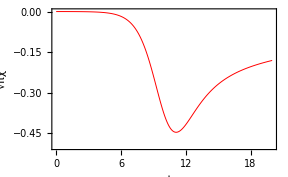

```mathematica
ListPlot[cv,option1]
```

```mathematica
Clear[cv1];
cv1=cv;
cv1⟦All,1⟧=init-cv1⟦All,1⟧;
```

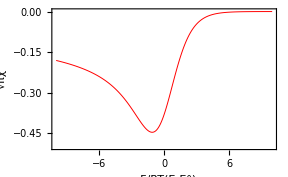

```mathematica
ListPlot[cv1,option2]
```

```mathematica
f=96485.3/(8.31451*298.15);

peakHeight=Min[cv1⟦All,2⟧];
Select[cv1,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧/f," V with height ",peakHeight]
```

peak at -0.028262 V with height -0.446113

## Anodic Sweep

Begin by calculating the continuation of the cathodic sweep.

```mathematica
Clear[init,switch,final,cv2,incr];

(*continuation of the cathodic sweep*)
init=10.;
switch=-10.;
final=2*(init-switch);
incr=0.05;

cv2=Table[{σt,-1/(2*Sqrt[Pi])*NIntegrate[Sqrt[σt-z]*Tanh[(init-z)/2]/(Cosh[(init-z)/2]^2),{z,0,σt}]},{σt,(init-switch),final,incr}];
```

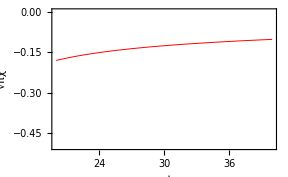

```mathematica
ListPlot[cv2,option3]
```

```mathematica
Clear[init,switch,final,incr,n,cv3];

(*anodic sweep*)
init=10.;
n=init-40.;
switch=-10.;
final=2*(init-switch);
incr=0.05(*incremental size of σt*);

cv3=Table[{σt,-1/(2*Sqrt[Pi])*NIntegrate[Sqrt[σt-z]*Tanh[(n+z)/2]/(Cosh[(n+z)/2]^2),{z,0,σt}]},{σt,(init-switch),final,incr}];
```

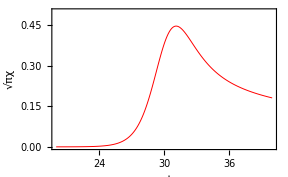

```mathematica
ListPlot[cv3,option4]
```

```mathematica
Clear[cv4];
cv4=cv2;
cv4[[All,2]]=cv4[[All,2]]+cv3[[All,2]];
```

## Combined Cathodic and Anodic Sweeps

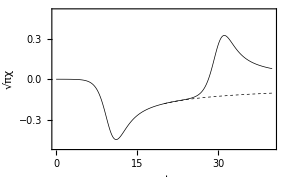

```mathematica
ListPlot[{cv,cv2,cv4},option5]
```

```mathematica
Clear[cv2a,cv4a];

cv2a=Table[{cv⟦j,1⟧-init,cv2⟦j,2⟧},{j,1,Length[cv2]}];

cv4a=Table[{cv⟦j,1⟧-init,cv4⟦j,2⟧},{j,1,Length[cv4]}];
```

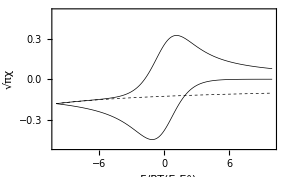

```mathematica
ListPlot[{cv1,cv2a,cv4a},option6]
```

## Spherical component

```mathematica
Clear[init,switch,incr,ξ,F,R,T,Subscript[r, o],υ,σ,𝒟,spherical1,spherical2];

init=10.(*= lnθ*);
switch=-10.;
incr=0.05;

ξ:=Exp[init-σt];
Subscript[r, o]=.1;
F=96485;
R=8.3144;
T=298;
υ=.05;
σ:=(F*υ)/(R*T);
𝒟=1.*^-5;

spherical1=Table[{σt,-1/(Subscript[r, o]*(1+ξ))*Sqrt[𝒟/σ]},{σt,0.,init-switch,incr}];
υ=.01;
spherical2=Table[{σt,-1/(Subscript[r, o]*(1+ξ))*Sqrt[𝒟/σ]},{σt,0.,init-switch,incr}];
```

```mathematica
combined1=MapThread[{(10-#1⟦1⟧),#2⟦2⟧+#1⟦2⟧}&,{cv,spherical1}];
```

```mathematica
combined2=MapThread[{(10-#1⟦1⟧),#2⟦2⟧+#1⟦2⟧}&,{cv,spherical2}];
```

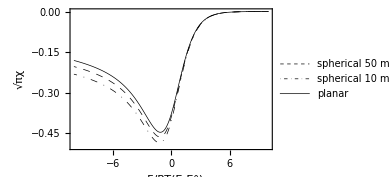

```mathematica
ListPlot[{combined1,combined2,cv1},option7,
PlotLegends->Placed[(Style[#,FontSize-> 11,FontFamily-> "Times New Roman"]&/@{"spherical 50 mV s^-1","spherical 10 mV s^-1","planar"}),After]]
```